```mathematica
i=1;
dataxy=Import[fileListxy[[i]]];
(*dataxy=Import[fileList[[i]]];*)
datat=Import[fileListt[[i]]];

trup= Max[Flatten[datat]];
tsrup=Ceiling[fac*Flatten[Position[Ceiling[Flatten[datat]],Ceiling[trup]]]];
ts=tsrup[[1]];

(*trup=Ceiling[0.60Dimensions[dataxy][[3]]];*)
trup=fac* Max[Flatten[datat]];



datasol=ListInterpolation[dataxy,{{0,L},{0,L},Flatten[datat]}];
```

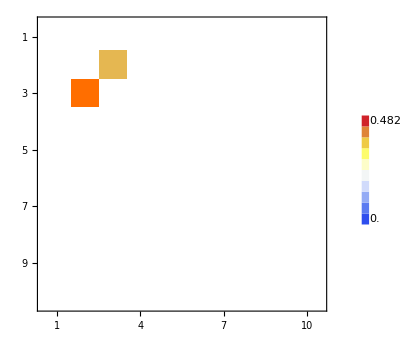

```mathematica
timeslice=tsrup[[1]];
FData1=Abs[Fourier[dataxy⟦All,All,timeslice⟧]];
FData1[[1,1]]=0;
norm1=Norm[FData1,"Frobenius"];
FData2=FData1/norm1;
thresh2=0.35Max[FData2];
FData=Threshold[FData2,{"Hard",thresh2}];
valmax=ToString[Max[FData[[1;;10,1;;10]]]];
valmin=ToString[Min[FData[[1;;10,1;;10]]]];;
dftCornerRup=
ShowLegend[
MatrixPlot[FData[[1;;10,1;;10]], BaseStyle->{FontWeight->"Plain",FontSize->25}],{ColorData["TemperatureMap"][1-#1]&,10,valmax,valmin,LegendPosition->{1.1,-.4}}
]
```